# Solving Equations Visually

This Mathematica notebook is licensed under a  
It creates the demonstrations used in my post XXXX

I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

## Definitions

```mathematica
op[x_,loc_]:=Text[Style[x,13,Bold,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_]:=Text[Style[x,13,weight,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_,color_]:=Text[Style[x,13,weight,color,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
sop[x_,loc_]:=Text[Style[x,13,Bold,Background->White,FontFamily->"Arial"],Scaled[loc]]
```

```mathematica
op["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
sop["x",{0,1}]
```

Text[x,Scaled[{0,1}]]

```mathematica
op["Plus\n" a+b,{0,0}]
```

Text[Plus
 a+b,{0,0}]

```mathematica
edge[loc1_,loc2_,sf_]:=Arrow[{loc1,loc2},Scaled[sf]]
```

```mathematica
spd=.0005
```

0.0005

```mathematica
mov[p_,q_,s_]:=(1-s)p+s q
```

## Visual statement

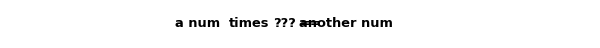

```mathematica
Graphics[{op["a num",Scaled[{.3,.5}]],
op["times",Scaled[{.4,.5}]],
op["???",Scaled[{.47,.5}]],op["==",Scaled[{.52,.5}]],
op["another num",Scaled[{.59,.5}]]},
ImageSize->600,AspectRatio->.07,PlotRange->{{-1,-1},{1,1}}]
```

```mathematica
outstring=StringJoin["\n",partitionstring,"\n",heightstring,"\n","Norm = ",ToString[mesh],"\n","Riemann Sum = ",ToString[Chop[sum]],"\n","Definite Integral = ",ToString[integralvalue]];
```

## Solving the equation using algebraic notation

```mathematica
Remove[s]
```

```mathematica
Graphics[{op["a",Scaled[{0,.5}]],
op["x",Scaled[{.25,.5}]],op["=",Scaled[{.5,.5}]],
op["b",Scaled[{.75,.5}]]},
AspectRatio->1,ImageSize->50]
```

-Graphics-

#### Bezier

```mathematica
g=BezierFunction[{{0,.5},{.4,-.2},{.8,.5-.14}}]
```

BezierFunction[{{0.,1.}},<>]

```mathematica
g[.3]
```

{0.24,0.1934}

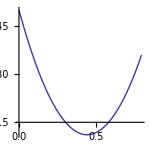

```mathematica
ParametricPlot[g[t], {t,0,1},ImageSize->150]
```

### This is VisualSolveAlgNotat.cfd

```mathematica
Text[Style[ToString[N[2/3 ,2]],TextAlignment->Right]]
```

0.67

<script type="text/javascript" src="http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js"></script>
<script type="text/javascript">
var cdf = new cdfplugin();
cdf.setDefaultContent('<a href="http://www.wolfram.com/cdf-player/"><img  src="VisualSolveAlgNotat.cfd.png"></a>');
cdf.embed('http://www.abstractmath.org/Mathematica/VisualSolveAlgNotat.cfd', 238, 157);
</script>

```mathematica
Manipulate[
Module[
{g=BezierFunction[{{0,.5},{.4,-.2},{.8,.5-.17}}]},
Show[
Graphics[
{
op["x",Scaled[{.25,.5}]],
op["==",Scaled[{.5,.5}]],
op[If[d<.55,"","—"],Scaled[{.8,.5}]],
op[b,Scaled[{.8,.5+.14d}]],
op[a,Scaled[g[d]]]
},
AspectRatio->1,ImageSize->50
]
]],
{{a,1},{1,2,3,4,5},ControlType->RadioButtonBar},{{b,1},{1,2,3,4,5},ControlType->RadioButtonBar},
{{d,0,""},0,1},
Paneled->False,SaveDefinitions->True
]
```

### This is VisualSolveTreeNotat

<script type="text/javascript" src="http://www.wolfram.com/cdf-player/plugin/v2.1/cdfplugin.js"></script>
<script type="text/javascript">
var cdf = new cdfplugin();
cdf.setDefaultContent('<a href="http://www.wolfram.com/cdf-player/"><img  src="VisualSolveTreeNotat.png"></a>');
cdf.embed('http://www.abstractmath.org/Mathematica/VisualSolveTreeNotat.cdf', 131, 194);
</script>

```mathematica
Manipulate[
If[c=="No",
Graphics[
{Arrowheads[0],
edge[{-1.5,0},{-1,1},spd],
edge[{.5,0},{-.5,2},spd],
edge[{-1,1},{-.5,2}, spd],
edge[{-.5,0},{-1,1},spd],
op["Equals",{-.5,2}],
op["Times",{-1,1}],
op["b",{.5,0}],
op["x",{-1.5,0}],
op["a",{-.5,0}]
},
Background->White,ImageSize->100,AspectRatio->1.2
],
Graphics[
{Arrowheads[0],
edge[{-.5,2},{0,1},spd],
edge[{.5,0},{0,1},spd],
edge[{-.5,0},{0,1},spd],
edge[{-1.5,0},{-.5,2}, spd],
op["Equals",{-.5,2}],
op["Divides",{0,1}],
op["b",{.5,0}],
op["x",{-1.5,0}],
op["a",{-.5,0}],
op["d",{-.35,.5}],op["n",{.35,.5}]
},
Background->White,ImageSize->100,AspectRatio->1.2
]
],
{{c,"No","move a"},{"No","Yes"},ControlType->RadioButtonBar},SaveDefinitions->True,Paneled->False]
```